```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/chrisonian/Code/GitHub/lcls2-lattice/bmad/models/hxr

```mathematica
plotopts = {Frame->True, BaseStyle->{FontSize->15}};
SetOptions[{ListPlot, ListContourPlot}, plotopts];
```

```mathematica
dat = Import["hxr_matching_twiss.dat", "Table"];
beta={#⟦2⟧, #⟦1⟧,#⟦3⟧}&/@dat;
alpha={#⟦2⟧, #⟦1⟧,#⟦4⟧}&/@dat;
```

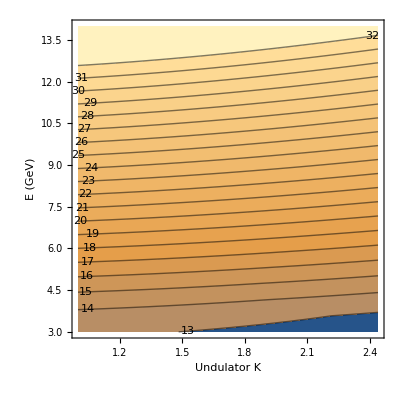

```mathematica
ListContourPlot[beta, FrameLabel->{ "Undulator K","E (GeV)", "Matching β_x, center of QF"},Contours->20, ContourLabels->All]
```

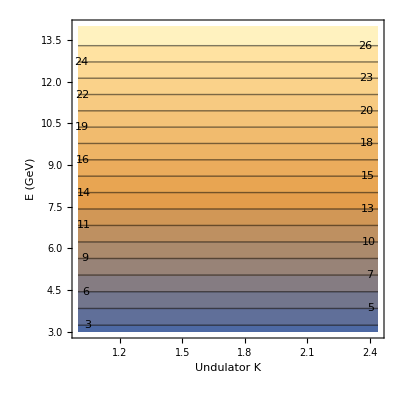

```mathematica
ListContourPlot[alpha, FrameLabel->{ "Undulator K","E (GeV)", "Matching β_y, center of QF"},Contours->20, ContourLabels->All]
```

```mathematica
8.400 3.57142
```

29.9999